# QMeSTools Showcase

## Load Package

```mathematica
(* Load the installed version of the package *)
Needs["QMeSderivation`"]
```

## Define the theory (a QCD truncation)

```mathematica
fRGEq = {
"Prefactor"->{1/2},
<|"type"->"Regulatordot", "indices"->{i,j}|>,
<|"type"->"Propagator", "indices"->{i,j}|>
};

fieldsQCD=<|
"bosonic"-> {
σ[p],(*sigma meson*)
Π[p,{a}],(*pions*)
 A[p,{v, c}](*gluon*)
},
 "fermionic"->{
{sb[p,{d,c}],s[p,{d,c}]},(*strange quark*)
{qb[p,{d,c,f}],q[p,{d,c,f}]},(*light quarks*)
{cb[p,{c}],c[p,{c}]}(*ghosts*)
}
|>;

TruncationQCD = {
{σ,σ},{Π,Π},{q,qb},{s,sb},{A,A},{c,cb},(* propagators *)
{qb,q,A},{cb,c,A},{sb,s,A},{A,A,A},{A,A,A,A},(* gluon sector scatterings *)
{qb,q,σ},{qb,q,Π},{qb,q,σ,σ},{qb,q,Π,Π},{qb,q,σ,Π},{qb,q,σ,σ,σ},{qb,q,σ,σ,Π},{qb,q,σ,Π,Π},{qb,q,Π,Π,Π}, (* quark-meson scatterings *)
 {σ,σ,σ},{σ,Π,Π},{σ,σ,σ,σ},{σ,σ,Π,Π},{Π,Π,Π,Π}(* meson scatterings *)
};

SetupfRGQCD= <|"MasterEquation"->fRGEq,
"FieldSpace"->fieldsQCD,
"Truncation"->TruncationQCD
|>;
```

## FRG Equations: Four-Quark vertex

### Derive flow equation of four-quark vertex

```mathematica
DerivativeListqbqqbq= {qb[p,{d4,c4,f4}],q[-p,{d3,c3,f3}],qb[p,{d2,c2,f2}],q[-p,{d1,c1,f1}]};
Diagramsqbqqbq=DeriveFunctionalEquation[SetupfRGQCD,DerivativeListqbqqbq,"OutputLevel"->"SuperindexDiagrams"];
Diagramsqbqqbq//Length
```

400

### Reduce the number of diagrams by using the symmetries of the tensor structure and the t-channel configuration

```mathematica
ReduceIdenticalFlowDiagrams::usage
```

ReduceIdenticalFlowDiagrams[diagrams,derivativeList,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.
The user has to supply the list of derivatives (i.e. external legs in the diagrams). Then, the symmetries are specified in the following way:
symmetries = {
	{ {1, 3}, Minus},
	{ {2, 4}, Minus}
	{ {1, 3}, {2, 4}, Plus},
}
Here, two antisymmetries (as specified by the Minus) are given, which consist of a single cycle each (1,3) and (2,4). These integers refer to the legs as given in derivativeList (in order).
ReduceIdenticalFlowDiagrams does not construct all symmetries from the given ones - therefore, the full symmetry group needs to be specified. Therefore, we also supply the symmetry consisting of both cycles explicitly in the third line.

```mathematica
symmetries={
{{1,3},Plus},
{{2,4},Plus},
{{1,3},{2,4},Plus}
};
DiagramsqbqqbqReduced=ReduceIdenticalFlowDiagrams[Diagramsqbqqbq,DerivativeListqbqqbq,symmetries];
DiagramsqbqqbqReduced//Length
```

61

### Plot the resulting diagrams

```mathematica
PlotSuperindexDiagram::usage
```

PlotSuperindexDiagram[diagram, setup, options]

Plot a single superindex diagram. The first argument to this function is the diagram itself, the second one is the corresponding QMeS setup.
The diagram has to be a superindex diagram.

The options for the function PlotSuperindexDiagram are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

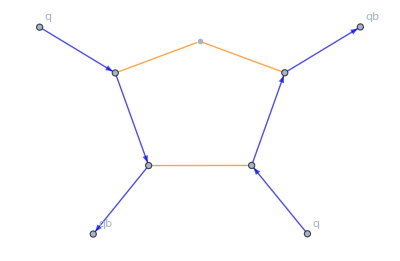
{4,-Graphics-}

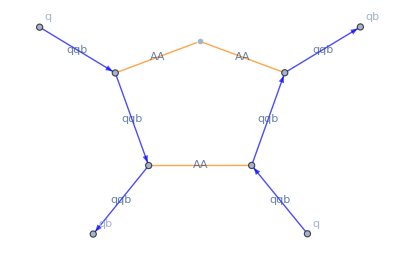
{4,-Graphics-}

```mathematica
PlotSuperindexDiagram[
DiagramsqbqqbqReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
PlotSuperindexDiagram[
DiagramsqbqqbqReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->True
]
```

```mathematica
PlotSuperindexDiagrams::usage
```

PlotSuperindexDiagram[diagrams, setup, options]

Plot a set of superindex diagrams. The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup.
The diagrams have to be superindex diagrams.

The options for the function PlotSuperindexDiagrams are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

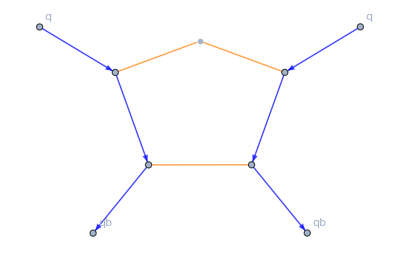
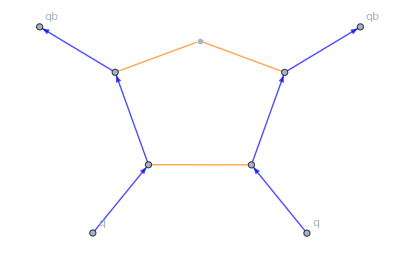
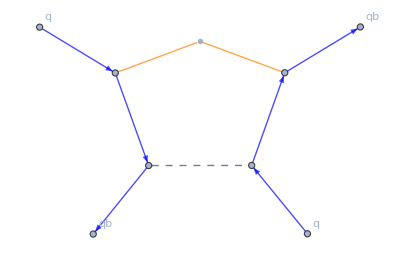
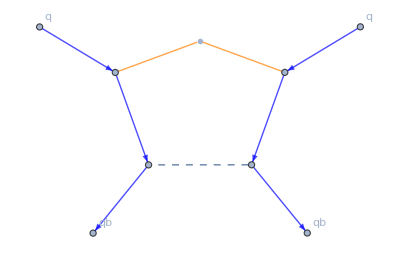
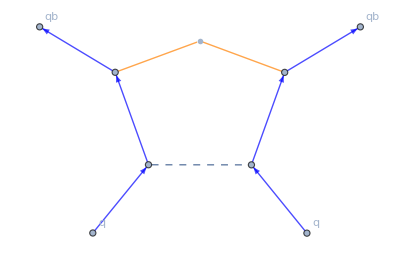
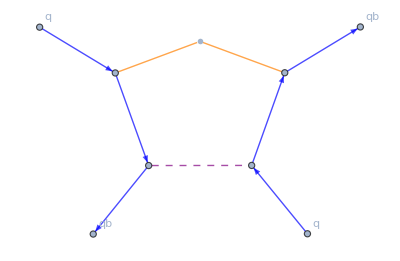
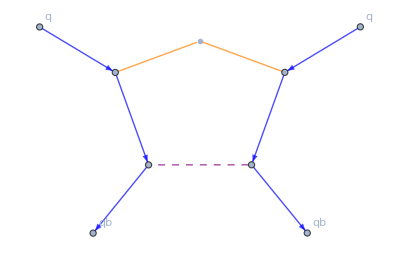
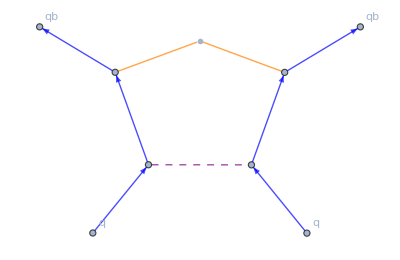
{{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-2,-Graphics-},{-2,-Graphics-},{-2,-Graphics-},{-2,-Graphics-}}

```mathematica
PlotSuperindexDiagrams[
DiagramsqbqqbqReduced,SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple},c->Dotted},
"ShowEdgeLabels"->False
]
```

### Get Full diagrams and reroute the momenta for use in finite T setups

```mathematica
RerouteFermionicMomenta::usage
```

RerouteFermionicMomenta[diagrams, setup, derivativeList]

Reroute external fermionic momenta in diagrams such that Matsubara frequencies are automatically correctly routed.
If a closed fermion loop is present, the momentum in this loop is marked by attaching the character 'f' to it (i.e. q -> qf in such a loop).
The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup. The third argument is the derivative list that has been used to derive the set of diagrams.
Be aware, that the rerouting exploits momentum conservation - therefore, one of the external momenta may be eliminated if this is not yet the case.

```mathematica
DiagramsqbqqbqFull=SuperindexToFullDiagrams[DiagramsqbqqbqReduced,SetupfRGQCD,DerivativeListqbqqbq];
RerouteFermionicMomenta[DiagramsqbqqbqFull,SetupfRGQCD,DerivativeListqbqqbq]
```

{{4 GAA[{-q,v$31965,c$31965,q,v$31923,c$31923}] GAA[{q,v$31927,c$31927,-q,v$31920,c$31920}] GAA[{q,v$31949,c$31949,-q,v$31943,c$31943}] Gqqb[{-p-q,d$31934,c$31934,f$31934,p+q,d$31939,c$31939,f$31939}] Gqqb[{-p-q,d$31956,c$31956,f$31956,p+q,d$31961,c$31961,f$31961}] RdotAA[{-q,v$31920,c$31920,q,v$31923,c$31923}] ΓAqbq[{-q,v$31943,c$31943,p+q,d$31939,c$31939,f$31939,-p,d3,c3,f3}] ΓAqbq[{-q,v$31965,c$31965,p+q,d$31961,c$31961,f$31961,-p,d1,c1,f1}] ΓAqbq[{q,v$31927,c$31927,p,d4,c4,f4,-p-q,d$31934,c$31934,f$31934}] ΓAqbq[{q,v$31949,c$31949,p,d2,c2,f2,-p-q,d$31956,c$31956,f$31956}]},{2 GAA[{-q,v$32068,c$32068,q,v$32026,c$32026}] GAA[{q,v$32030,c$32030,-q,v$32023,c$32023}] GAA[{q,v$32052,c$32052,-q,v$32046,c$32046}] Gqqb[{-p-q,d$32059,c$32059,f$32059,p+q,d$32064,c$32064,f$32064}] Gqqb[{-p+q,d$32041,c$32041,f$32041,p-q,d$32036,c$32036,f$32036}] RdotAA[{-q,v$32023,c$32023,q,v$32026,c$32026}] ΓAqbq[{-q,v$32046,c$32046,p,d4,c4,f4,-p+q,d$32041,c$32041,f$32041}] ΓAqbq[{-q,v$32068,c$32068,p+q,d$32064,c$32064,f$32064,-p,d1,c1,f1}] ΓAqbq[{q,v$32030,c$32030,p-q,d$32036,c$32036,f$32036,-p,d3,c3,f3}] ΓAqbq[{q,v$32052,c$32052,p,d2,c2,f2,-p-q,d$32059,c$32059,f$32059}]},{-2 GAA[{-q,v$32144,c$32144,q,v$32151,c$32151}] GAA[{-q,v$32166,c$32166,q,v$32124,c$32124}] GAA[{q,v$32128,c$32128,-q,v$32121,c$32121}] Gqqb[{-p-q,d$32135,c$32135,f$32135,p+q,d$32140,c$32140,f$32140}] Gqqb[{-p+q,d$32161,c$32161,f$32161,p-q,d$32156,c$32156,f$32156}] RdotAA[{-q,v$32121,c$32121,q,v$32124,c$32124}] ΓAqbq[{-q,v$32144,c$32144,p+q,d$32140,c$32140,f$32140,-p,d3,c3,f3}] ΓAqbq[{-q,v$32166,c$32166,p,d4,c4,f4,-p+q,d$32161,c$32161,f$32161}] ΓAqbq[{q,v$32128,c$32128,p,d2,c2,f2,-p-q,d$32135,c$32135,f$32135}] ΓAqbq[{q,v$32151,c$32151,p-q,d$32156,c$32156,f$32156,-p,d1,c1,f1}]},{4 GAA[{-q,v$32264,c$32264,q,v$32222,c$32222}] GAA[{q,v$32226,c$32226,-q,v$32219,c$32219}] Gqqb[{-p-q,d$32233,c$32233,f$32233,p+q,d$32238,c$32238,f$32238}] Gqqb[{-p-q,d$32255,c$32255,f$32255,p+q,d$32260,c$32260,f$32260}] GΠΠ[{q,a$32248,-q,a$32242}] RdotAA[{-q,v$32219,c$32219,q,v$32222,c$32222}] ΓAqbq[{-q,v$32264,c$32264,p+q,d$32260,c$32260,f$32260,-p,d1,c1,f1}] ΓAqbq[{q,v$32226,c$32226,p,d4,c4,f4,-p-q,d$32233,c$32233,f$32233}] ΓΠqbq[{-q,a$32242,p+q,d$32238,c$32238,f$32238,-p,d3,c3,f3}] ΓΠqbq[{q,a$32248,p,d2,c2,f2,-p-q,d$32255,c$32255,f$32255}]},{2 GAA[{-q,v$32362,c$32362,q,v$32320,c$32320}] GAA[{q,v$32324,c$32324,-q,v$32317,c$32317}] Gqqb[{-p-q,d$32353,c$32353,f$32353,p+q,d$32358,c$32358,f$32358}] Gqqb[{-p+q,d$32335,c$32335,f$32335,p-q,d$32330,c$32330,f$32330}] GΠΠ[{q,a$32346,-q,a$32340}] RdotAA[{-q,v$32317,c$32317,q,v$32320,c$32320}] ΓAqbq[{-q,v$32362,c$32362,p+q,d$32358,c$32358,f$32358,-p,d1,c1,f1}] ΓAqbq[{q,v$32324,c$32324,p-q,d$32330,c$32330,f$32330,-p,d3,c3,f3}] ΓΠqbq[{-q,a$32340,p,d4,c4,f4,-p+q,d$32335,c$32335,f$32335}] ΓΠqbq[{q,a$32346,p,d2,c2,f2,-p-q,d$32353,c$32353,f$32353}]},{-2 GAA[{-q,v$32460,c$32460,q,v$32418,c$32418}] GAA[{q,v$32422,c$32422,-q,v$32415,c$32415}] Gqqb[{-p-q,d$32429,c$32429,f$32429,p+q,d$32434,c$32434,f$32434}] Gqqb[{-p+q,d$32455,c$32455,f$32455,p-q,d$32450,c$32450,f$32450}] GΠΠ[{-q,a$32438,q,a$32445}] RdotAA[{-q,v$32415,c$32415,q,v$32418,c$32418}] ΓAqbq[{-q,v$32460,c$32460,p,d4,c4,f4,-p+q,d$32455,c$32455,f$32455}] ΓAqbq[{q,v$32422,c$32422,p,d2,c2,f2,-p-q,d$32429,c$32429,f$32429}] ΓΠqbq[{-q,a$32438,p+q,d$32434,c$32434,f$32434,-p,d3,c3,f3}] ΓΠqbq[{q,a$32445,p-q,d$32450,c$32450,f$32450,-p,d1,c1,f1}]},{4 GAA[{-q,v$32556,c$32556,q,v$32516,c$32516}] GAA[{q,v$32520,c$32520,-q,v$32513,c$32513}] Gqqb[{-p-q,d$32527,c$32527,f$32527,p+q,d$32532,c$32532,f$32532}] Gqqb[{-p-q,d$32547,c$32547,f$32547,p+q,d$32552,c$32552,f$32552}] Gσσ[{q,-q}] RdotAA[{-q,v$32513,c$32513,q,v$32516,c$32516}] ΓAqbq[{-q,v$32556,c$32556,p+q,d$32552,c$32552,f$32552,-p,d1,c1,f1}] ΓAqbq[{q,v$32520,c$32520,p,d4,c4,f4,-p-q,d$32527,c$32527,f$32527}] Γσqbq[{-q,p+q,d$32532,c$32532,f$32532,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$32547,c$32547,f$32547}]},{2 GAA[{-q,v$32652,c$32652,q,v$32612,c$32612}] GAA[{q,v$32616,c$32616,-q,v$32609,c$32609}] Gqqb[{-p-q,d$32643,c$32643,f$32643,p+q,d$32648,c$32648,f$32648}] Gqqb[{-p+q,d$32627,c$32627,f$32627,p-q,d$32622,c$32622,f$32622}] Gσσ[{q,-q}] RdotAA[{-q,v$32609,c$32609,q,v$32612,c$32612}] ΓAqbq[{-q,v$32652,c$32652,p+q,d$32648,c$32648,f$32648,-p,d1,c1,f1}] ΓAqbq[{q,v$32616,c$32616,p-q,d$32622,c$32622,f$32622,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$32627,c$32627,f$32627}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$32643,c$32643,f$32643}]},{-2 GAA[{-q,v$32748,c$32748,q,v$32708,c$32708}] GAA[{q,v$32712,c$32712,-q,v$32705,c$32705}] Gqqb[{-p-q,d$32719,c$32719,f$32719,p+q,d$32724,c$32724,f$32724}] Gqqb[{-p+q,d$32743,c$32743,f$32743,p-q,d$32738,c$32738,f$32738}] Gσσ[{-q,q}] RdotAA[{-q,v$32705,c$32705,q,v$32708,c$32708}] ΓAqbq[{-q,v$32748,c$32748,p,d4,c4,f4,-p+q,d$32743,c$32743,f$32743}] ΓAqbq[{q,v$32712,c$32712,p,d2,c2,f2,-p-q,d$32719,c$32719,f$32719}] Γσqbq[{-q,p+q,d$32724,c$32724,f$32724,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$32738,c$32738,f$32738,-p,d1,c1,f1}]},{-4 GAA[{-q,v$32835,c$32835,q,v$32842,c$32842}] GAA[{q,v$32819,c$32819,-q,v$32813,c$32813}] Gqqb[{-p+q,d$32804,c$32804,f$32804,p-q,d$32847,c$32847,f$32847}] Gqqb[{-p+q,d$32808,c$32808,f$32808,p-q,d$32801,c$32801,f$32801}] Gqqb[{-p+q,d$32830,c$32830,f$32830,p-q,d$32825,c$32825,f$32825}] Rdotqbq[{p-q,d$32801,c$32801,f$32801,-p+q,d$32804,c$32804,f$32804}] ΓAqbq[{-q,v$32813,c$32813,p,d4,c4,f4,-p+q,d$32808,c$32808,f$32808}] ΓAqbq[{-q,v$32835,c$32835,p,d2,c2,f2,-p+q,d$32830,c$32830,f$32830}] ΓAqbq[{q,v$32819,c$32819,p-q,d$32825,c$32825,f$32825,-p,d3,c3,f3}] ΓAqbq[{q,v$32842,c$32842,p-q,d$32847,c$32847,f$32847,-p,d1,c1,f1}]},{-4 GAA[{-q,v$32933,c$32933,q,v$32940,c$32940}] GAA[{q,v$32917,c$32917,-q,v$32911,c$32911}] Gqqb[{-p-q,d$32924,c$32924,f$32924,p+q,d$32929,c$32929,f$32929}] Gqqb[{-p+q,d$32902,c$32902,f$32902,p-q,d$32945,c$32945,f$32945}] Gqqb[{-p+q,d$32906,c$32906,f$32906,p-q,d$32899,c$32899,f$32899}] Rdotqbq[{p-q,d$32899,c$32899,f$32899,-p+q,d$32902,c$32902,f$32902}] ΓAqbq[{-q,v$32911,c$32911,p,d4,c4,f4,-p+q,d$32906,c$32906,f$32906}] ΓAqbq[{-q,v$32933,c$32933,p+q,d$32929,c$32929,f$32929,-p,d3,c3,f3}] ΓAqbq[{q,v$32917,c$32917,p,d2,c2,f2,-p-q,d$32924,c$32924,f$32924}] ΓAqbq[{q,v$32940,c$32940,p-q,d$32945,c$32945,f$32945,-p,d1,c1,f1}]},{-4 GAA[{q,v$33015,c$33015,-q,v$33009,c$33009}] Gqqb[{-p+q,d$33000,c$33000,f$33000,p-q,d$33043,c$33043,f$33043}] Gqqb[{-p+q,d$33004,c$33004,f$33004,p-q,d$32997,c$32997,f$32997}] Gqqb[{-p+q,d$33026,c$33026,f$33026,p-q,d$33021,c$33021,f$33021}] GΠΠ[{-q,a$33031,q,a$33038}] Rdotqbq[{p-q,d$32997,c$32997,f$32997,-p+q,d$33000,c$33000,f$33000}] ΓAqbq[{-q,v$33009,c$33009,p,d4,c4,f4,-p+q,d$33004,c$33004,f$33004}] ΓAqbq[{q,v$33015,c$33015,p-q,d$33021,c$33021,f$33021,-p,d3,c3,f3}] ΓΠqbq[{-q,a$33031,p,d2,c2,f2,-p+q,d$33026,c$33026,f$33026}] ΓΠqbq[{q,a$33038,p-q,d$33043,c$33043,f$33043,-p,d1,c1,f1}]},{-4 GAA[{-q,v$33129,c$33129,q,v$33136,c$33136}] Gqqb[{-p+q,d$33098,c$33098,f$33098,p-q,d$33141,c$33141,f$33141}] Gqqb[{-p+q,d$33102,c$33102,f$33102,p-q,d$33095,c$33095,f$33095}] Gqqb[{-p+q,d$33124,c$33124,f$33124,p-q,d$33119,c$33119,f$33119}] GΠΠ[{q,a$33113,-q,a$33107}] Rdotqbq[{p-q,d$33095,c$33095,f$33095,-p+q,d$33098,c$33098,f$33098}] ΓAqbq[{-q,v$33129,c$33129,p,d2,c2,f2,-p+q,d$33124,c$33124,f$33124}] ΓAqbq[{q,v$33136,c$33136,p-q,d$33141,c$33141,f$33141,-p,d1,c1,f1}] ΓΠqbq[{-q,a$33107,p,d4,c4,f4,-p+q,d$33102,c$33102,f$33102}] ΓΠqbq[{q,a$33113,p-q,d$33119,c$33119,f$33119,-p,d3,c3,f3}]},{-4 GAA[{q,v$33211,c$33211,-q,v$33205,c$33205}] Gqqb[{-p-q,d$33218,c$33218,f$33218,p+q,d$33223,c$33223,f$33223}] Gqqb[{-p+q,d$33196,c$33196,f$33196,p-q,d$33239,c$33239,f$33239}] Gqqb[{-p+q,d$33200,c$33200,f$33200,p-q,d$33193,c$33193,f$33193}] GΠΠ[{-q,a$33227,q,a$33234}] Rdotqbq[{p-q,d$33193,c$33193,f$33193,-p+q,d$33196,c$33196,f$33196}] ΓAqbq[{-q,v$33205,c$33205,p,d4,c4,f4,-p+q,d$33200,c$33200,f$33200}] ΓAqbq[{q,v$33211,c$33211,p,d2,c2,f2,-p-q,d$33218,c$33218,f$33218}] ΓΠqbq[{-q,a$33227,p+q,d$33223,c$33223,f$33223,-p,d3,c3,f3}] ΓΠqbq[{q,a$33234,p-q,d$33239,c$33239,f$33239,-p,d1,c1,f1}]},{-4 GAA[{-q,v$33325,c$33325,q,v$33332,c$33332}] Gqqb[{-p-q,d$33316,c$33316,f$33316,p+q,d$33321,c$33321,f$33321}] Gqqb[{-p+q,d$33294,c$33294,f$33294,p-q,d$33337,c$33337,f$33337}] Gqqb[{-p+q,d$33298,c$33298,f$33298,p-q,d$33291,c$33291,f$33291}] GΠΠ[{q,a$33309,-q,a$33303}] Rdotqbq[{p-q,d$33291,c$33291,f$33291,-p+q,d$33294,c$33294,f$33294}] ΓAqbq[{-q,v$33325,c$33325,p+q,d$33321,c$33321,f$33321,-p,d3,c3,f3}] ΓAqbq[{q,v$33332,c$33332,p-q,d$33337,c$33337,f$33337,-p,d1,c1,f1}] ΓΠqbq[{-q,a$33303,p,d4,c4,f4,-p+q,d$33298,c$33298,f$33298}] ΓΠqbq[{q,a$33309,p,d2,c2,f2,-p-q,d$33316,c$33316,f$33316}]},{-4 GAA[{q,v$33407,c$33407,-q,v$33401,c$33401}] Gqqb[{-p+q,d$33392,c$33392,f$33392,p-q,d$33433,c$33433,f$33433}] Gqqb[{-p+q,d$33396,c$33396,f$33396,p-q,d$33389,c$33389,f$33389}] Gqqb[{-p+q,d$33418,c$33418,f$33418,p-q,d$33413,c$33413,f$33413}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$33389,c$33389,f$33389,-p+q,d$33392,c$33392,f$33392}] ΓAqbq[{-q,v$33401,c$33401,p,d4,c4,f4,-p+q,d$33396,c$33396,f$33396}] ΓAqbq[{q,v$33407,c$33407,p-q,d$33413,c$33413,f$33413,-p,d3,c3,f3}] Γσqbq[{-q,p,d2,c2,f2,-p+q,d$33418,c$33418,f$33418}] Γσqbq[{q,p-q,d$33433,c$33433,f$33433,-p,d1,c1,f1}]},{-4 GAA[{-q,v$33517,c$33517,q,v$33524,c$33524}] Gqqb[{-p+q,d$33488,c$33488,f$33488,p-q,d$33529,c$33529,f$33529}] Gqqb[{-p+q,d$33492,c$33492,f$33492,p-q,d$33485,c$33485,f$33485}] Gqqb[{-p+q,d$33512,c$33512,f$33512,p-q,d$33507,c$33507,f$33507}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$33485,c$33485,f$33485,-p+q,d$33488,c$33488,f$33488}] ΓAqbq[{-q,v$33517,c$33517,p,d2,c2,f2,-p+q,d$33512,c$33512,f$33512}] ΓAqbq[{q,v$33524,c$33524,p-q,d$33529,c$33529,f$33529,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$33492,c$33492,f$33492}] Γσqbq[{q,p-q,d$33507,c$33507,f$33507,-p,d3,c3,f3}]},{-4 GAA[{q,v$33599,c$33599,-q,v$33593,c$33593}] Gqqb[{-p-q,d$33606,c$33606,f$33606,p+q,d$33611,c$33611,f$33611}] Gqqb[{-p+q,d$33584,c$33584,f$33584,p-q,d$33625,c$33625,f$33625}] Gqqb[{-p+q,d$33588,c$33588,f$33588,p-q,d$33581,c$33581,f$33581}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$33581,c$33581,f$33581,-p+q,d$33584,c$33584,f$33584}] ΓAqbq[{-q,v$33593,c$33593,p,d4,c4,f4,-p+q,d$33588,c$33588,f$33588}] ΓAqbq[{q,v$33599,c$33599,p,d2,c2,f2,-p-q,d$33606,c$33606,f$33606}] Γσqbq[{-q,p+q,d$33611,c$33611,f$33611,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$33625,c$33625,f$33625,-p,d1,c1,f1}]},{-4 GAA[{-q,v$33709,c$33709,q,v$33716,c$33716}] Gqqb[{-p-q,d$33700,c$33700,f$33700,p+q,d$33705,c$33705,f$33705}] Gqqb[{-p+q,d$33680,c$33680,f$33680,p-q,d$33721,c$33721,f$33721}] Gqqb[{-p+q,d$33684,c$33684,f$33684,p-q,d$33677,c$33677,f$33677}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$33677,c$33677,f$33677,-p+q,d$33680,c$33680,f$33680}] ΓAqbq[{-q,v$33709,c$33709,p+q,d$33705,c$33705,f$33705,-p,d3,c3,f3}] ΓAqbq[{q,v$33716,c$33716,p-q,d$33721,c$33721,f$33721,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$33684,c$33684,f$33684}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$33700,c$33700,f$33700}]},{-4 Gqqb[{-p+q,d$33776,c$33776,f$33776,p-q,d$33819,c$33819,f$33819}] Gqqb[{-p+q,d$33780,c$33780,f$33780,p-q,d$33773,c$33773,f$33773}] Gqqb[{-p+q,d$33802,c$33802,f$33802,p-q,d$33797,c$33797,f$33797}] GΠΠ[{-q,a$33807,q,a$33814}] GΠΠ[{q,a$33791,-q,a$33785}] Rdotqbq[{p-q,d$33773,c$33773,f$33773,-p+q,d$33776,c$33776,f$33776}] ΓΠqbq[{-q,a$33785,p,d4,c4,f4,-p+q,d$33780,c$33780,f$33780}] ΓΠqbq[{-q,a$33807,p,d2,c2,f2,-p+q,d$33802,c$33802,f$33802}] ΓΠqbq[{q,a$33791,p-q,d$33797,c$33797,f$33797,-p,d3,c3,f3}] ΓΠqbq[{q,a$33814,p-q,d$33819,c$33819,f$33819,-p,d1,c1,f1}]},{-4 Gqqb[{-p-q,d$33896,c$33896,f$33896,p+q,d$33901,c$33901,f$33901}] Gqqb[{-p+q,d$33874,c$33874,f$33874,p-q,d$33917,c$33917,f$33917}] Gqqb[{-p+q,d$33878,c$33878,f$33878,p-q,d$33871,c$33871,f$33871}] GΠΠ[{-q,a$33905,q,a$33912}] GΠΠ[{q,a$33889,-q,a$33883}] Rdotqbq[{p-q,d$33871,c$33871,f$33871,-p+q,d$33874,c$33874,f$33874}] ΓΠqbq[{-q,a$33883,p,d4,c4,f4,-p+q,d$33878,c$33878,f$33878}] ΓΠqbq[{-q,a$33905,p+q,d$33901,c$33901,f$33901,-p,d3,c3,f3}] ΓΠqbq[{q,a$33889,p,d2,c2,f2,-p-q,d$33896,c$33896,f$33896}] ΓΠqbq[{q,a$33912,p-q,d$33917,c$33917,f$33917,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$33972,c$33972,f$33972,p-q,d$34013,c$34013,f$34013}] Gqqb[{-p+q,d$33976,c$33976,f$33976,p-q,d$33969,c$33969,f$33969}] Gqqb[{-p+q,d$33998,c$33998,f$33998,p-q,d$33993,c$33993,f$33993}] GΠΠ[{q,a$33987,-q,a$33981}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$33969,c$33969,f$33969,-p+q,d$33972,c$33972,f$33972}] ΓΠqbq[{-q,a$33981,p,d4,c4,f4,-p+q,d$33976,c$33976,f$33976}] ΓΠqbq[{q,a$33987,p-q,d$33993,c$33993,f$33993,-p,d3,c3,f3}] Γσqbq[{-q,p,d2,c2,f2,-p+q,d$33998,c$33998,f$33998}] Γσqbq[{q,p-q,d$34013,c$34013,f$34013,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$34068,c$34068,f$34068,p-q,d$34109,c$34109,f$34109}] Gqqb[{-p+q,d$34072,c$34072,f$34072,p-q,d$34065,c$34065,f$34065}] Gqqb[{-p+q,d$34092,c$34092,f$34092,p-q,d$34087,c$34087,f$34087}] GΠΠ[{-q,a$34097,q,a$34104}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$34065,c$34065,f$34065,-p+q,d$34068,c$34068,f$34068}] ΓΠqbq[{-q,a$34097,p,d2,c2,f2,-p+q,d$34092,c$34092,f$34092}] ΓΠqbq[{q,a$34104,p-q,d$34109,c$34109,f$34109,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$34072,c$34072,f$34072}] Γσqbq[{q,p-q,d$34087,c$34087,f$34087,-p,d3,c3,f3}]},{-4 Gqqb[{-p-q,d$34186,c$34186,f$34186,p+q,d$34191,c$34191,f$34191}] Gqqb[{-p+q,d$34164,c$34164,f$34164,p-q,d$34205,c$34205,f$34205}] Gqqb[{-p+q,d$34168,c$34168,f$34168,p-q,d$34161,c$34161,f$34161}] GΠΠ[{q,a$34179,-q,a$34173}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$34161,c$34161,f$34161,-p+q,d$34164,c$34164,f$34164}] ΓΠqbq[{-q,a$34173,p,d4,c4,f4,-p+q,d$34168,c$34168,f$34168}] ΓΠqbq[{q,a$34179,p,d2,c2,f2,-p-q,d$34186,c$34186,f$34186}] Γσqbq[{-q,p+q,d$34191,c$34191,f$34191,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$34205,c$34205,f$34205,-p,d1,c1,f1}]},{-4 Gqqb[{-p-q,d$34280,c$34280,f$34280,p+q,d$34285,c$34285,f$34285}] Gqqb[{-p+q,d$34260,c$34260,f$34260,p-q,d$34301,c$34301,f$34301}] Gqqb[{-p+q,d$34264,c$34264,f$34264,p-q,d$34257,c$34257,f$34257}] GΠΠ[{-q,a$34289,q,a$34296}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$34257,c$34257,f$34257,-p+q,d$34260,c$34260,f$34260}] ΓΠqbq[{-q,a$34289,p+q,d$34285,c$34285,f$34285,-p,d3,c3,f3}] ΓΠqbq[{q,a$34296,p-q,d$34301,c$34301,f$34301,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$34264,c$34264,f$34264}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$34280,c$34280,f$34280}]},{-4 Gqqb[{-p+q,d$34356,c$34356,f$34356,p-q,d$34395,c$34395,f$34395}] Gqqb[{-p+q,d$34360,c$34360,f$34360,p-q,d$34353,c$34353,f$34353}] Gqqb[{-p+q,d$34380,c$34380,f$34380,p-q,d$34375,c$34375,f$34375}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$34353,c$34353,f$34353,-p+q,d$34356,c$34356,f$34356}] Γσqbq[{-q,p,d2,c2,f2,-p+q,d$34380,c$34380,f$34380}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$34360,c$34360,f$34360}] Γσqbq[{q,p-q,d$34375,c$34375,f$34375,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$34395,c$34395,f$34395,-p,d1,c1,f1}]},{-4 Gqqb[{-p-q,d$34470,c$34470,f$34470,p+q,d$34475,c$34475,f$34475}] Gqqb[{-p+q,d$34450,c$34450,f$34450,p-q,d$34489,c$34489,f$34489}] Gqqb[{-p+q,d$34454,c$34454,f$34454,p-q,d$34447,c$34447,f$34447}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$34447,c$34447,f$34447,-p+q,d$34450,c$34450,f$34450}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$34454,c$34454,f$34454}] Γσqbq[{-q,p+q,d$34475,c$34475,f$34475,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$34470,c$34470,f$34470}] Γσqbq[{q,p-q,d$34489,c$34489,f$34489,-p,d1,c1,f1}]},{4 GAA[{q,v$34570,c$34570,-q,v$34564,c$34564}] Gqqb[{-p-q,d$34555,c$34555,f$34555,p+q,d$34560,c$34560,f$34560}] Gqqb[{-p-q,d$34577,c$34577,f$34577,p+q,d$34582,c$34582,f$34582}] GΠΠ[{-q,a$34586,q,a$34544}] GΠΠ[{q,a$34548,-q,a$34541}] RdotΠΠ[{-q,a$34541,q,a$34544}] ΓAqbq[{-q,v$34564,c$34564,p+q,d$34560,c$34560,f$34560,-p,d3,c3,f3}] ΓAqbq[{q,v$34570,c$34570,p,d2,c2,f2,-p-q,d$34577,c$34577,f$34577}] ΓΠqbq[{-q,a$34586,p+q,d$34582,c$34582,f$34582,-p,d1,c1,f1}] ΓΠqbq[{q,a$34548,p,d4,c4,f4,-p-q,d$34555,c$34555,f$34555}]},{2 GAA[{q,v$34668,c$34668,-q,v$34662,c$34662}] Gqqb[{-p-q,d$34675,c$34675,f$34675,p+q,d$34680,c$34680,f$34680}] Gqqb[{-p+q,d$34657,c$34657,f$34657,p-q,d$34652,c$34652,f$34652}] GΠΠ[{-q,a$34684,q,a$34642}] GΠΠ[{q,a$34646,-q,a$34639}] RdotΠΠ[{-q,a$34639,q,a$34642}] ΓAqbq[{-q,v$34662,c$34662,p,d4,c4,f4,-p+q,d$34657,c$34657,f$34657}] ΓAqbq[{q,v$34668,c$34668,p,d2,c2,f2,-p-q,d$34675,c$34675,f$34675}] ΓΠqbq[{-q,a$34684,p+q,d$34680,c$34680,f$34680,-p,d1,c1,f1}] ΓΠqbq[{q,a$34646,p-q,d$34652,c$34652,f$34652,-p,d3,c3,f3}]},{-2 GAA[{-q,v$34760,c$34760,q,v$34767,c$34767}] Gqqb[{-p-q,d$34751,c$34751,f$34751,p+q,d$34756,c$34756,f$34756}] Gqqb[{-p+q,d$34777,c$34777,f$34777,p-q,d$34772,c$34772,f$34772}] GΠΠ[{-q,a$34782,q,a$34740}] GΠΠ[{q,a$34744,-q,a$34737}] RdotΠΠ[{-q,a$34737,q,a$34740}] ΓAqbq[{-q,v$34760,c$34760,p+q,d$34756,c$34756,f$34756,-p,d3,c3,f3}] ΓAqbq[{q,v$34767,c$34767,p-q,d$34772,c$34772,f$34772,-p,d1,c1,f1}] ΓΠqbq[{-q,a$34782,p,d4,c4,f4,-p+q,d$34777,c$34777,f$34777}] ΓΠqbq[{q,a$34744,p,d2,c2,f2,-p-q,d$34751,c$34751,f$34751}]},{4 Gqqb[{-p-q,d$34849,c$34849,f$34849,p+q,d$34854,c$34854,f$34854}] Gqqb[{-p-q,d$34871,c$34871,f$34871,p+q,d$34876,c$34876,f$34876}] GΠΠ[{-q,a$34880,q,a$34838}] GΠΠ[{q,a$34842,-q,a$34835}] GΠΠ[{q,a$34864,-q,a$34858}] RdotΠΠ[{-q,a$34835,q,a$34838}] ΓΠqbq[{-q,a$34858,p+q,d$34854,c$34854,f$34854,-p,d3,c3,f3}] ΓΠqbq[{-q,a$34880,p+q,d$34876,c$34876,f$34876,-p,d1,c1,f1}] ΓΠqbq[{q,a$34842,p,d4,c4,f4,-p-q,d$34849,c$34849,f$34849}] ΓΠqbq[{q,a$34864,p,d2,c2,f2,-p-q,d$34871,c$34871,f$34871}]},{2 Gqqb[{-p-q,d$34969,c$34969,f$34969,p+q,d$34974,c$34974,f$34974}] Gqqb[{-p+q,d$34951,c$34951,f$34951,p-q,d$34946,c$34946,f$34946}] GΠΠ[{-q,a$34978,q,a$34936}] GΠΠ[{q,a$34940,-q,a$34933}] GΠΠ[{q,a$34962,-q,a$34956}] RdotΠΠ[{-q,a$34933,q,a$34936}] ΓΠqbq[{-q,a$34956,p,d4,c4,f4,-p+q,d$34951,c$34951,f$34951}] ΓΠqbq[{-q,a$34978,p+q,d$34974,c$34974,f$34974,-p,d1,c1,f1}] ΓΠqbq[{q,a$34940,p-q,d$34946,c$34946,f$34946,-p,d3,c3,f3}] ΓΠqbq[{q,a$34962,p,d2,c2,f2,-p-q,d$34969,c$34969,f$34969}]},{-2 Gqqb[{-p-q,d$35045,c$35045,f$35045,p+q,d$35050,c$35050,f$35050}] Gqqb[{-p+q,d$35071,c$35071,f$35071,p-q,d$35066,c$35066,f$35066}] GΠΠ[{-q,a$35054,q,a$35061}] GΠΠ[{-q,a$35076,q,a$35034}] GΠΠ[{q,a$35038,-q,a$35031}] RdotΠΠ[{-q,a$35031,q,a$35034}] ΓΠqbq[{-q,a$35054,p+q,d$35050,c$35050,f$35050,-p,d3,c3,f3}] ΓΠqbq[{-q,a$35076,p,d4,c4,f4,-p+q,d$35071,c$35071,f$35071}] ΓΠqbq[{q,a$35038,p,d2,c2,f2,-p-q,d$35045,c$35045,f$35045}] ΓΠqbq[{q,a$35061,p-q,d$35066,c$35066,f$35066,-p,d1,c1,f1}]},{4 Gqqb[{-p-q,d$35143,c$35143,f$35143,p+q,d$35148,c$35148,f$35148}] Gqqb[{-p-q,d$35163,c$35163,f$35163,p+q,d$35168,c$35168,f$35168}] GΠΠ[{-q,a$35172,q,a$35132}] GΠΠ[{q,a$35136,-q,a$35129}] Gσσ[{q,-q}] RdotΠΠ[{-q,a$35129,q,a$35132}] ΓΠqbq[{-q,a$35172,p+q,d$35168,c$35168,f$35168,-p,d1,c1,f1}] ΓΠqbq[{q,a$35136,p,d4,c4,f4,-p-q,d$35143,c$35143,f$35143}] Γσqbq[{-q,p+q,d$35148,c$35148,f$35148,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$35163,c$35163,f$35163}]},{2 Gqqb[{-p-q,d$35259,c$35259,f$35259,p+q,d$35264,c$35264,f$35264}] Gqqb[{-p+q,d$35243,c$35243,f$35243,p-q,d$35238,c$35238,f$35238}] GΠΠ[{-q,a$35268,q,a$35228}] GΠΠ[{q,a$35232,-q,a$35225}] Gσσ[{q,-q}] RdotΠΠ[{-q,a$35225,q,a$35228}] ΓΠqbq[{-q,a$35268,p+q,d$35264,c$35264,f$35264,-p,d1,c1,f1}] ΓΠqbq[{q,a$35232,p-q,d$35238,c$35238,f$35238,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$35243,c$35243,f$35243}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$35259,c$35259,f$35259}]},{-2 Gqqb[{-p-q,d$35335,c$35335,f$35335,p+q,d$35340,c$35340,f$35340}] Gqqb[{-p+q,d$35359,c$35359,f$35359,p-q,d$35354,c$35354,f$35354}] GΠΠ[{-q,a$35364,q,a$35324}] GΠΠ[{q,a$35328,-q,a$35321}] Gσσ[{-q,q}] RdotΠΠ[{-q,a$35321,q,a$35324}] ΓΠqbq[{-q,a$35364,p,d4,c4,f4,-p+q,d$35359,c$35359,f$35359}] ΓΠqbq[{q,a$35328,p,d2,c2,f2,-p-q,d$35335,c$35335,f$35335}] Γσqbq[{-q,p+q,d$35340,c$35340,f$35340,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$35354,c$35354,f$35354,-p,d1,c1,f1}]},{4 GAA[{q,v$35443,c$35443,-q,v$35437,c$35437}] Gqqb[{-p-q,d$35428,c$35428,f$35428,p+q,d$35433,c$35433,f$35433}] Gqqb[{-p-q,d$35450,c$35450,f$35450,p+q,d$35455,c$35455,f$35455}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓAqbq[{-q,v$35437,c$35437,p+q,d$35433,c$35433,f$35433,-p,d3,c3,f3}] ΓAqbq[{q,v$35443,c$35443,p,d2,c2,f2,-p-q,d$35450,c$35450,f$35450}] Γσqbq[{-q,p+q,d$35455,c$35455,f$35455,-p,d1,c1,f1}] Γσqbq[{q,p,d4,c4,f4,-p-q,d$35428,c$35428,f$35428}]},{2 GAA[{q,v$35537,c$35537,-q,v$35531,c$35531}] Gqqb[{-p-q,d$35544,c$35544,f$35544,p+q,d$35549,c$35549,f$35549}] Gqqb[{-p+q,d$35526,c$35526,f$35526,p-q,d$35521,c$35521,f$35521}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓAqbq[{-q,v$35531,c$35531,p,d4,c4,f4,-p+q,d$35526,c$35526,f$35526}] ΓAqbq[{q,v$35537,c$35537,p,d2,c2,f2,-p-q,d$35544,c$35544,f$35544}] Γσqbq[{-q,p+q,d$35549,c$35549,f$35549,-p,d1,c1,f1}] Γσqbq[{q,p-q,d$35521,c$35521,f$35521,-p,d3,c3,f3}]},{-2 GAA[{-q,v$35625,c$35625,q,v$35632,c$35632}] Gqqb[{-p-q,d$35616,c$35616,f$35616,p+q,d$35621,c$35621,f$35621}] Gqqb[{-p+q,d$35642,c$35642,f$35642,p-q,d$35637,c$35637,f$35637}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓAqbq[{-q,v$35625,c$35625,p+q,d$35621,c$35621,f$35621,-p,d3,c3,f3}] ΓAqbq[{q,v$35632,c$35632,p-q,d$35637,c$35637,f$35637,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$35642,c$35642,f$35642}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$35616,c$35616,f$35616}]},{4 Gqqb[{-p-q,d$35710,c$35710,f$35710,p+q,d$35715,c$35715,f$35715}] Gqqb[{-p-q,d$35732,c$35732,f$35732,p+q,d$35737,c$35737,f$35737}] GΠΠ[{q,a$35725,-q,a$35719}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{-q,a$35719,p+q,d$35715,c$35715,f$35715,-p,d3,c3,f3}] ΓΠqbq[{q,a$35725,p,d2,c2,f2,-p-q,d$35732,c$35732,f$35732}] Γσqbq[{-q,p+q,d$35737,c$35737,f$35737,-p,d1,c1,f1}] Γσqbq[{q,p,d4,c4,f4,-p-q,d$35710,c$35710,f$35710}]},{2 Gqqb[{-p-q,d$35826,c$35826,f$35826,p+q,d$35831,c$35831,f$35831}] Gqqb[{-p+q,d$35808,c$35808,f$35808,p-q,d$35803,c$35803,f$35803}] GΠΠ[{q,a$35819,-q,a$35813}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{-q,a$35813,p,d4,c4,f4,-p+q,d$35808,c$35808,f$35808}] ΓΠqbq[{q,a$35819,p,d2,c2,f2,-p-q,d$35826,c$35826,f$35826}] Γσqbq[{-q,p+q,d$35831,c$35831,f$35831,-p,d1,c1,f1}] Γσqbq[{q,p-q,d$35803,c$35803,f$35803,-p,d3,c3,f3}]},{-2 Gqqb[{-p-q,d$35898,c$35898,f$35898,p+q,d$35903,c$35903,f$35903}] Gqqb[{-p+q,d$35924,c$35924,f$35924,p-q,d$35919,c$35919,f$35919}] GΠΠ[{-q,a$35907,q,a$35914}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{-q,a$35907,p+q,d$35903,c$35903,f$35903,-p,d3,c3,f3}] ΓΠqbq[{q,a$35914,p-q,d$35919,c$35919,f$35919,-p,d1,c1,f1}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$35924,c$35924,f$35924}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$35898,c$35898,f$35898}]},{4 Gqqb[{-p-q,d$35992,c$35992,f$35992,p+q,d$35997,c$35997,f$35997}] Gqqb[{-p-q,d$36012,c$36012,f$36012,p+q,d$36017,c$36017,f$36017}] Gσσ[{-q,q}] Gσσ[{q,-q}]^2 Rdotσσ[{-q,q}] Γσqbq[{-q,p+q,d$35997,c$35997,f$35997,-p,d3,c3,f3}] Γσqbq[{-q,p+q,d$36017,c$36017,f$36017,-p,d1,c1,f1}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$36012,c$36012,f$36012}] Γσqbq[{q,p,d4,c4,f4,-p-q,d$35992,c$35992,f$35992}]},{2 Gqqb[{-p-q,d$36104,c$36104,f$36104,p+q,d$36109,c$36109,f$36109}] Gqqb[{-p+q,d$36088,c$36088,f$36088,p-q,d$36083,c$36083,f$36083}] Gσσ[{-q,q}] Gσσ[{q,-q}]^2 Rdotσσ[{-q,q}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$36088,c$36088,f$36088}] Γσqbq[{-q,p+q,d$36109,c$36109,f$36109,-p,d1,c1,f1}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$36104,c$36104,f$36104}] Γσqbq[{q,p-q,d$36083,c$36083,f$36083,-p,d3,c3,f3}]},{-2 Gqqb[{-p-q,d$36176,c$36176,f$36176,p+q,d$36181,c$36181,f$36181}] Gqqb[{-p+q,d$36200,c$36200,f$36200,p-q,d$36195,c$36195,f$36195}] Gσσ[{-q,q}]^2 Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$36200,c$36200,f$36200}] Γσqbq[{-q,p+q,d$36181,c$36181,f$36181,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$36176,c$36176,f$36176}] Γσqbq[{q,p-q,d$36195,c$36195,f$36195,-p,d1,c1,f1}]},{4 Gqqb[{-p-q,d$36283,c$36283,f$36283,p+q,d$36288,c$36288,f$36288}] GΠΠ[{-q,a$36292,q,a$36260}] GΠΠ[{q,a$36264,-q,a$36257}] GΠΠ[{q,a$36276,-q,a$36270}] RdotΠΠ[{-q,a$36257,q,a$36260}] ΓΠqbq[{-q,a$36292,p+q,d$36288,c$36288,f$36288,-p,d1,c1,f1}] ΓΠqbq[{q,a$36276,p,d2,c2,f2,-p-q,d$36283,c$36283,f$36283}] ΓΠΠqbq[{q,a$36264,-q,a$36270,p,d4,c4,f4,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$36367,c$36367,f$36367,p-q,d$36362,c$36362,f$36362}] GΠΠ[{-q,a$36350,q,a$36357}] GΠΠ[{-q,a$36372,q,a$36340}] GΠΠ[{q,a$36344,-q,a$36337}] RdotΠΠ[{-q,a$36337,q,a$36340}] ΓΠqbq[{-q,a$36372,p,d4,c4,f4,-p+q,d$36367,c$36367,f$36367}] ΓΠqbq[{q,a$36357,p-q,d$36362,c$36362,f$36362,-p,d1,c1,f1}] ΓΠΠqbq[{q,a$36344,-q,a$36350,p,d2,c2,f2,-p,d3,c3,f3}]},{4 Gqqb[{-p-q,d$36441,c$36441,f$36441,p+q,d$36446,c$36446,f$36446}] GΠΠ[{-q,a$36450,q,a$36420}] GΠΠ[{q,a$36424,-q,a$36417}] Gσσ[{q,-q}] RdotΠΠ[{-q,a$36417,q,a$36420}] ΓΠqbq[{-q,a$36450,p+q,d$36446,c$36446,f$36446,-p,d1,c1,f1}] ΓΠσqbq[{q,a$36424,-q,p,d4,c4,f4,-p,d3,c3,f3}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$36441,c$36441,f$36441}]},{-4 Gqqb[{-p+q,d$36523,c$36523,f$36523,p-q,d$36518,c$36518,f$36518}] GΠΠ[{-q,a$36528,q,a$36498}] GΠΠ[{q,a$36502,-q,a$36495}] Gσσ[{-q,q}] RdotΠΠ[{-q,a$36495,q,a$36498}] ΓΠqbq[{-q,a$36528,p,d4,c4,f4,-p+q,d$36523,c$36523,f$36523}] ΓΠσqbq[{q,a$36502,-q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$36518,c$36518,f$36518,-p,d1,c1,f1}]},{4 Gqqb[{-p-q,d$36596,c$36596,f$36596,p+q,d$36601,c$36601,f$36601}] GΠΠ[{q,a$36589,-q,a$36582}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{q,a$36589,p,d2,c2,f2,-p-q,d$36596,c$36596,f$36596}] ΓΠσqbq[{-q,a$36582,q,p,d4,c4,f4,-p,d3,c3,f3}] Γσqbq[{-q,p+q,d$36601,c$36601,f$36601,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$36676,c$36676,f$36676,p-q,d$36671,c$36671,f$36671}] GΠΠ[{-q,a$36658,q,a$36666}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠqbq[{q,a$36666,p-q,d$36671,c$36671,f$36671,-p,d1,c1,f1}] ΓΠσqbq[{-q,a$36658,q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$36676,c$36676,f$36676}]},{4 Gqqb[{-p-q,d$36746,c$36746,f$36746,p+q,d$36751,c$36751,f$36751}] Gσσ[{-q,q}] Gσσ[{q,-q}]^2 Rdotσσ[{-q,q}] Γσqbq[{-q,p+q,d$36751,c$36751,f$36751,-p,d1,c1,f1}] Γσqbq[{q,p,d2,c2,f2,-p-q,d$36746,c$36746,f$36746}] Γσσqbq[{q,-q,p,d4,c4,f4,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$36824,c$36824,f$36824,p-q,d$36819,c$36819,f$36819}] Gσσ[{-q,q}]^2 Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$36824,c$36824,f$36824}] Γσqbq[{q,p-q,d$36819,c$36819,f$36819,-p,d1,c1,f1}] Γσσqbq[{q,-q,p,d2,c2,f2,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$36876,c$36876,f$36876,p-q,d$36909,c$36909,f$36909}] Gqqb[{-p+q,d$36880,c$36880,f$36880,p-q,d$36873,c$36873,f$36873}] GΠΠ[{-q,a$36897,q,a$36904}] GΠΠ[{q,a$36891,-q,a$36885}] Rdotqbq[{p-q,d$36873,c$36873,f$36873,-p+q,d$36876,c$36876,f$36876}] ΓΠqbq[{-q,a$36885,p,d4,c4,f4,-p+q,d$36880,c$36880,f$36880}] ΓΠqbq[{q,a$36904,p-q,d$36909,c$36909,f$36909,-p,d1,c1,f1}] ΓΠΠqbq[{q,a$36891,-q,a$36897,p,d2,c2,f2,-p,d3,c3,f3}]},{-4 Gqqb[{-p+q,d$36956,c$36956,f$36956,p-q,d$36987,c$36987,f$36987}] Gqqb[{-p+q,d$36960,c$36960,f$36960,p-q,d$36953,c$36953,f$36953}] GΠΠ[{q,a$36971,-q,a$36965}] Gσσ[{-q,q}] Rdotqbq[{p-q,d$36953,c$36953,f$36953,-p+q,d$36956,c$36956,f$36956}] ΓΠqbq[{-q,a$36965,p,d4,c4,f4,-p+q,d$36960,c$36960,f$36960}] ΓΠσqbq[{q,a$36971,-q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{q,p-q,d$36987,c$36987,f$36987,-p,d1,c1,f1}]},{-4 Gqqb[{-p+q,d$37034,c$37034,f$37034,p-q,d$37065,c$37065,f$37065}] Gqqb[{-p+q,d$37038,c$37038,f$37038,p-q,d$37031,c$37031,f$37031}] GΠΠ[{-q,a$37052,q,a$37060}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$37031,c$37031,f$37031,-p+q,d$37034,c$37034,f$37034}] ΓΠqbq[{q,a$37060,p-q,d$37065,c$37065,f$37065,-p,d1,c1,f1}] ΓΠσqbq[{-q,a$37052,q,p,d2,c2,f2,-p,d3,c3,f3}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$37038,c$37038,f$37038}]},{-4 Gqqb[{-p+q,d$37112,c$37112,f$37112,p-q,d$37141,c$37141,f$37141}] Gqqb[{-p+q,d$37116,c$37116,f$37116,p-q,d$37109,c$37109,f$37109}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotqbq[{p-q,d$37109,c$37109,f$37109,-p+q,d$37112,c$37112,f$37112}] Γσqbq[{-q,p,d4,c4,f4,-p+q,d$37116,c$37116,f$37116}] Γσqbq[{q,p-q,d$37141,c$37141,f$37141,-p,d1,c1,f1}] Γσσqbq[{q,-q,p,d2,c2,f2,-p,d3,c3,f3}]},{-2 GΠΠ[{-q,a$37198,q,a$37205}] GΠΠ[{-q,a$37210,q,a$37188}] GΠΠ[{q,a$37192,-q,a$37185}] RdotΠΠ[{-q,a$37185,q,a$37188}] ΓΠΠqbq[{q,a$37192,-q,a$37198,p,d2,c2,f2,-p,d3,c3,f3}] ΓΠΠqbq[{q,a$37205,-q,a$37210,p,d4,c4,f4,-p,d1,c1,f1}]},{-2 GΠΠ[{-q,a$37269,q,a$37250}] GΠΠ[{q,a$37254,-q,a$37247}] Gσσ[{-q,q}] RdotΠΠ[{-q,a$37247,q,a$37250}] ΓΠσqbq[{-q,a$37269,q,p,d4,c4,f4,-p,d1,c1,f1}] ΓΠσqbq[{q,a$37254,-q,p,d2,c2,f2,-p,d3,c3,f3}]},{-2 GΠΠ[{-q,a$37316,q,a$37324}] Gσσ[{-q,q}] Gσσ[{q,-q}] Rdotσσ[{-q,q}] ΓΠσqbq[{-q,a$37316,q,p,d2,c2,f2,-p,d3,c3,f3}] ΓΠσqbq[{q,a$37324,-q,p,d4,c4,f4,-p,d1,c1,f1}]},{-2 Gσσ[{-q,q}]^2 Gσσ[{q,-q}] Rdotσσ[{-q,q}] Γσσqbq[{q,-q,p,d2,c2,f2,-p,d3,c3,f3}] Γσσqbq[{q,-q,p,d4,c4,f4,-p,d1,c1,f1}]}}

## FRG Equations: Three-gluon vertex

### Derive flow equation of three-gluon vertex

```mathematica
DerivativeListAAA= {A[p1,{v1,c1}],A[p2,{v3,c3}],A[p3,{v3,c3}]};
DiagramsAAA=DeriveFunctionalEquation[SetupfRGQCD,DerivativeListAAA,"OutputLevel"->"SuperindexDiagrams"];
DiagramsAAA//Length
```

48

### Reduce the number of diagrams on the symmetric point

```mathematica
ReduceIdenticalFlowDiagrams::usage
```

ReduceIdenticalFlowDiagrams[diagrams,derivativeList,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.
The user has to supply the list of derivatives (i.e. external legs in the diagrams). Then, the symmetries are specified in the following way:
symmetries = {
	{ {1, 3}, Minus},
	{ {2, 4}, Minus}
	{ {1, 3}, {2, 4}, Plus},
}
Here, two antisymmetries (as specified by the Minus) are given, which consist of a single cycle each (1,3) and (2,4). These integers refer to the legs as given in derivativeList (in order).
ReduceIdenticalFlowDiagrams does not construct all symmetries from the given ones - therefore, the full symmetry group needs to be specified. Therefore, we also supply the symmetry consisting of both cycles explicitly in the third line.

```mathematica
symmetries={
{{1,2},Plus},
{{2,3},Plus},
{{3,1},Plus},
{{1,2,3},Plus},
{{3,2,1},Plus}
};
DiagramsAAAReduced=ReduceIdenticalFlowDiagrams[DiagramsAAA,DerivativeListAAA,symmetries];
DiagramsAAAReduced//Length
```

5

### Plot the resulting diagrams

```mathematica
PlotSuperindexDiagram::usage
```

PlotSuperindexDiagram[diagram, setup, options]

Plot a single superindex diagram. The first argument to this function is the diagram itself, the second one is the corresponding QMeS setup.
The diagram has to be a superindex diagram.

The options for the function PlotSuperindexDiagram are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

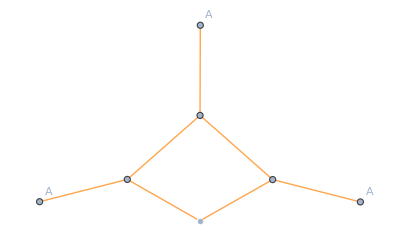
{-3,-Graphics-}

```mathematica
PlotSuperindexDiagram[
DiagramsAAAReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
```

```mathematica
PlotSuperindexDiagrams::usage
```

PlotSuperindexDiagram[diagrams, setup, options]

Plot a set of superindex diagrams. The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup.
The diagrams have to be superindex diagrams.

The options for the function PlotSuperindexDiagrams are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}.

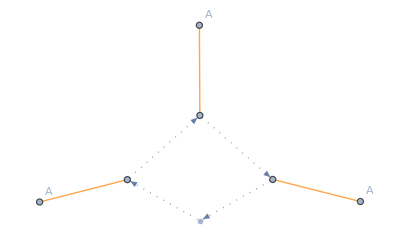
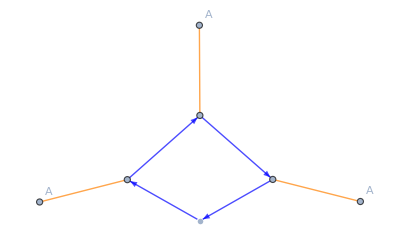
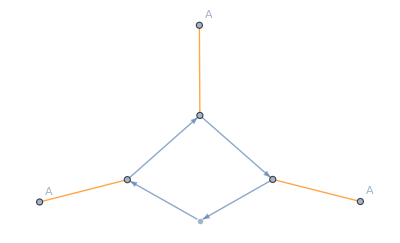
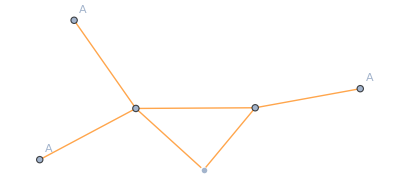
{{-3,-Graphics-},{-6,-Graphics-},{-6,-Graphics-},{-6,-Graphics-},{3,-Graphics-}}

```mathematica
PlotSuperindexDiagrams[
DiagramsAAAReduced,SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple},c->Dotted},
"ShowEdgeLabels"->False
]
```

### Get Full diagrams and reroute the momenta for use in finite T setups

```mathematica
RerouteFermionicMomenta::usage
```

RerouteFermionicMomenta[diagrams, setup, derivativeList]

Reroute external fermionic momenta in diagrams such that Matsubara frequencies are automatically correctly routed.
If a closed fermion loop is present, the momentum in this loop is marked by attaching the character 'f' to it (i.e. q -> qf in such a loop).
The first argument to this function is a list of diagrams, the second one is the corresponding QMeS setup. The third argument is the derivative list that has been used to derive the set of diagrams.
Be aware, that the rerouting exploits momentum conservation - therefore, one of the external momenta may be eliminated if this is not yet the case.

```mathematica
DiagramsAAAFull=SuperindexToFullDiagrams[DiagramsAAAReduced,SetupfRGQCD,DerivativeListAAA];
RerouteFermionicMomenta[DiagramsAAAFull,SetupfRGQCD,DerivativeListAAA]
```

{{-3 GAA[{p3-q,v$44301,c$44301,-p3+q,v$44307,c$44307}] GAA[{-q,v$44312,c$44312,q,v$44280,c$44280}] GAA[{q,v$44284,c$44284,-q,v$44277,c$44277}] GAA[{-p2-p3+q,v$44295,c$44295,p2+p3-q,v$44290,c$44290}] RdotAA[{-q,v$44277,c$44277,q,v$44280,c$44280}] ΓAAA[{q,v$44284,c$44284,p2+p3-q,v$44290,c$44290,-p2-p3,v1,c1}] ΓAAA[{-p3+q,v$44307,c$44307,-q,v$44312,c$44312,p3,v3,c3}] ΓAAA[{-p2-p3+q,v$44295,c$44295,p3-q,v$44301,c$44301,p2,v3,c3}]},{-6 Gccb[{qf,c$44359,-qf,c$44364}] Gccb[{qf,c$44392,-qf,c$44356}] Gccb[{p3+qf,c$44381,-p3-qf,c$44386}] Gccb[{p2+p3+qf,c$44370,-p2-p3-qf,c$44375}] Rdotcbc[{-qf,c$44356,qf,c$44359}] ΓAcbc[{p2,v3,c3,-p2-p3-qf,c$44375,p3+qf,c$44381}] ΓAcbc[{-p2-p3,v1,c1,-qf,c$44364,p2+p3+qf,c$44370}] ΓAcbc[{p3,v3,c3,-p3-qf,c$44386,qf,c$44392}]},{-6 Gqqb[{qf,d$44438,c$44438,f$44438,-qf,d$44443,c$44443,f$44443}] Gqqb[{qf,d$44471,c$44471,f$44471,-qf,d$44435,c$44435,f$44435}] Gqqb[{p3+qf,d$44460,c$44460,f$44460,-p3-qf,d$44465,c$44465,f$44465}] Gqqb[{p2+p3+qf,d$44449,c$44449,f$44449,-p2-p3-qf,d$44454,c$44454,f$44454}] Rdotqbq[{-qf,d$44435,c$44435,f$44435,qf,d$44438,c$44438,f$44438}] ΓAqbq[{p2,v3,c3,-p2-p3-qf,d$44454,c$44454,f$44454,p3+qf,d$44460,c$44460,f$44460}] ΓAqbq[{-p2-p3,v1,c1,-qf,d$44443,c$44443,f$44443,p2+p3+qf,d$44449,c$44449,f$44449}] ΓAqbq[{p3,v3,c3,-p3-qf,d$44465,c$44465,f$44465,qf,d$44471,c$44471,f$44471}]},{-6 Gssb[{qf,d$44517,c$44517,-qf,d$44522,c$44522}] Gssb[{qf,d$44550,c$44550,-qf,d$44514,c$44514}] Gssb[{p3+qf,d$44539,c$44539,-p3-qf,d$44544,c$44544}] Gssb[{p2+p3+qf,d$44528,c$44528,-p2-p3-qf,d$44533,c$44533}] Rdotsbs[{-qf,d$44514,c$44514,qf,d$44517,c$44517}] ΓAsbs[{p2,v3,c3,-p2-p3-qf,d$44533,c$44533,p3+qf,d$44539,c$44539}] ΓAsbs[{-p2-p3,v1,c1,-qf,d$44522,c$44522,p2+p3+qf,d$44528,c$44528}] ΓAsbs[{p3,v3,c3,-p3-qf,d$44544,c$44544,qf,d$44550,c$44550}]},{3 GAA[{p3-q,v$44606,c$44606,-p3+q,v$44613,c$44613}] GAA[{-q,v$44618,c$44618,q,v$44596,c$44596}] GAA[{q,v$44600,c$44600,-q,v$44593,c$44593}] RdotAA[{-q,v$44593,c$44593,q,v$44596,c$44596}] ΓAAA[{-p3+q,v$44613,c$44613,-q,v$44618,c$44618,p3,v3,c3}] ΓAAAA[{q,v$44600,c$44600,p3-q,v$44606,c$44606,-p2-p3,v1,c1,p2,v3,c3}]}}